# Liver slices MFA

```mathematica
<<NilssonLab`MetabolicNetwork`
<<NilssonLab`ExtremePathways`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
<<NilssonLab`Visualization`
```

```mathematica
<<NilssonLab`OpenFLUX`
```

```mathematica
<<NilssonLab`IsotopeDistributions`
```

## Set paths

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport

```mathematica
patientId="L002";
```

```mathematica
experimentId="Human_liver_"<>patientId
```

Human_liver_L002

```mathematica
modelId="liver-model-working"
```

liver-model-working

```mathematica
lcmsDataDir="C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\lcms-data";
```

## Import model

```mathematica
OpenDBConnection[]
```

### Import from OpenFLUX format

We only keep the network model from OpenFLUX. (Targets are set from data)

```mathematica
net=First@OpenFLUXImport["liver-model_openflux.txt"];
```

Boundary network

```mathematica
bnet=BoundaryNetwork[net]
```

<BoundaryNetwork, 35 boundary fluxes>

### Check against network from database

```mathematica
dbNet=NetworkFromDB[modelId];
```

```mathematica
TrueQ[net==dbNet]
```

True

### Get atom map from database

All atom transitions for reactions in model

```mathematica
atomMap=AtomMapsFromDB[net,{"C"}];
atomMap=RenumberAtoms[RemoveUnreachable[net,atomMap]];
Length[atomMap]
```

89

Consistency check. Missing data for cofactors is okay at this stage as long as they are removed below.

```mathematica
CheckAtomMap[atomMap]
```

{}

Create boundary atom maps (only needed for uptake reactions!)

```mathematica
bmap=BoundaryAtomMaps[net,atomMap];
bmap//Length
```

35

Reactions without atom maps

```mathematica
Extract[Reactions[net],Position[AtomList/@atomMap,{}]]
```

{<Reaction ADK1>,<Reaction ATPS4m>,<Reaction ATPtm(rev)>,<Reaction CELLWORK>,<Reaction CRNtim>,<Reaction CYOOm>,<Reaction CYOR-u10m>,<Reaction H2Oter>,<Reaction H2Otm(rev)>,<Reaction Htm2(rev)>,<Reaction NADH2-u10m>,<Reaction NADH_REDOX>,<Reaction NDPK1>,<Reaction NH4tm(rev)>,<Reaction O2tm>,<Reaction PIt2m>,<Reaction PIter>,<Reaction PPA>}

### Symmetry

```mathematica
symmetry=GetSymmetryMap[atomMap]
```

{fum→{{1,2},{3,4}},succ→{{1,2},{3,4}}}

## Import LCMS data

### From peak area data

Import peak areas. We do not normalize at this step since peak areas are needed for uptake/release measurements

```mathematica
{measuredMetIds,sampleIds,measuredMIDs}=ImportMIDTable[FileNameJoin[{lcmsDataDir,"L002",experimentId<>"_peakareas_ambiguous_met.tsv"}]];
```

```mathematica
measuredMetIds
```

{{glc-D},{ala-L},{arg-L},{asn-L},{asp-L},{Lcystin},{gln-L},{his-L},{leu-L},{ile-L},{lys-L},{met-L},{phe-L},{pro-L},{ser-L},{thr-L},{trp-L},{tyr-L},{val-L},{mal-L},{f6p,g1p,g6p},{dhap,g3p},{r5p},{udpg},{creat},{orn},{citr-L},{gudac},{glyc3p},{akg},{succ},{glu-L},{gly}}

### Targets

Define targets from measured metabolites present in the model

```mathematica
targets=Cases[MetaboliteEMUs[atomMap],EMU[Metabolite[Alternatives@@Flatten[measuredMetIds],__],_]]
```

{<akg_c{(12345)}>,<akg_m{(12345)}>,<ala-L_c{(123)}>,<arg-L_c{(123456)}>,<asp-L_c{(1234)}>,<asp-L_m{(1234)}>,<citr-L_c{(123456)}>,<citr-L_m{(123456)}>,<dhap_c{(123)}>,<f6p_c{(123456)}>,<g1p_r{(123456)}>,<g3p_c{(123)}>,<g6p_c{(123456)}>,<g6p_r{(123456)}>,<glc-D_c{(123456)}>,<glc-D_r{(123456)}>,<gln-L_c{(12345)}>,<gln-L_m{(12345)}>,<glu-L_c{(12345)}>,<glu-L_m{(12345)}>,<gly_c{(12)}>,<glyc3p_c{(123)}>,<mal-L_c{(1234)}>,<mal-L_m{(1234)}>,<orn_c{(12345)}>,<orn_m{(12345)}>,<ser-L_c{(123)}>,<succ_m{(1234)}>}

Drop any measured metabolites not in the model

```mathematica
Complement[Flatten[measuredMetIds],MetaboliteID/@Metabolite/@targets]
```

{asn-L,creat,gudac,his-L,ile-L,Lcystin,leu-L,lys-L,met-L,phe-L,pro-L,r5p,thr-L,trp-L,tyr-L,udpg,val-L}

```mathematica
Block[{ix},
ix=DeleteDuplicates[
First/@Position[measuredMetIds,Alternatives@@(MetaboliteID/@Metabolite/@targets)]];
measuredMIDs=measuredMIDs⟦ix⟧;
measuredMetIds=measuredMetIds⟦ix⟧;]
```

```mathematica
Length[measuredMetIds]
```

16

List of unique names for measurements, for use with GAMS

```mathematica
measuredMetNames=Map[ListToString[#,"__"]&,measuredMetIds]
```

{glc-D,ala-L,arg-L,asp-L,gln-L,ser-L,mal-L,f6p__g1p__g6p,dhap__g3p,orn,citr-L,glyc3p,akg,succ,glu-L,gly}

### EMU mixing matrix

Create (measurements x targets) mixing matrix

```mathematica
emuMixing=SparseArray[
Join@@Table[
Thread[Rule[
Thread[{i,Flatten[Position[targets,EMU[Metabolite[Alternatives@@measuredMetIds⟦i⟧,_,_],_]]]}],
1]],
{i,Length[measuredMetIds]}],
{Length[measuredMetIds],Length[targets]}]
```

SparseArray[<28>, {16, 28}]

Normalize rows to 1

```mathematica
emuMixing=SparseArray[emuMixing/(Total/@emuMixing)];
```

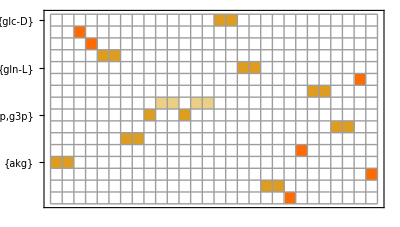

```mathematica
MatrixPlot[emuMixing,
FrameTicks->{Transpose[{Range[Length[measuredMetIds]],measuredMetIds}],None},Mesh->True]
```

List of measurement-target mappings

```mathematica
TableForm[Replace[
NonZeroIndices[emuMixing],
{i_,j_}:>{measuredMetNames⟦i⟧,targets⟦j⟧},{1}]]
```

glc-D | <glc-D_c{(123456)}>
glc-D | <glc-D_r{(123456)}>
ala-L | <ala-L_c{(123)}>
arg-L | <arg-L_c{(123456)}>
asp-L | <asp-L_c{(1234)}>
asp-L | <asp-L_m{(1234)}>
gln-L | <gln-L_c{(12345)}>
gln-L | <gln-L_m{(12345)}>
ser-L | <ser-L_c{(123)}>
mal-L | <mal-L_c{(1234)}>
mal-L | <mal-L_m{(1234)}>
f6p__g1p__g6p | <f6p_c{(123456)}>
f6p__g1p__g6p | <g1p_r{(123456)}>
f6p__g1p__g6p | <g6p_c{(123456)}>
f6p__g1p__g6p | <g6p_r{(123456)}>
dhap__g3p | <dhap_c{(123)}>
dhap__g3p | <g3p_c{(123)}>
orn | <orn_c{(12345)}>
orn | <orn_m{(12345)}>
citr-L | <citr-L_c{(123456)}>
citr-L | <citr-L_m{(123456)}>
glyc3p | <glyc3p_c{(123)}>
akg | <akg_c{(12345)}>
akg | <akg_m{(12345)}>
succ | <succ_m{(1234)}>
glu-L | <glu-L_c{(12345)}>
glu-L | <glu-L_m{(12345)}>
gly | <gly_c{(12)}>

### Sample annotations

For QC checks

Import as a rule table

```mathematica
sampleInfo=Import[
FileNameJoin[{lcmsDataDir,patientId,experimentId<>"_sampleinfo.tsv"}]];
sampleInfoFactors=Rest[First[sampleInfo]];
sampleInfo=Rest[sampleInfo ];
```

```mathematica
sampleInfo=Replace[sampleIds,Map[Rule[First[#],Rest[#]]&,sampleInfo],{1}]
```

{{tissue slice 0h,tissue extract,,L002,,human},{tissue slice 0h,tissue extract,,L002,,human},{tissue slice 0h,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,13C,L002,1,human},{tissue slice 24h,tissue extract,13C,L002,,human},{tissue slice 24h,tissue extract,13C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 24h,medium,13C,L002,1,human},{spent medium 24h,medium,13C,L002,,human},{spent medium 24h,medium,13C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{fresh medium 0h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 0h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{,plasma,,L002,,human}}

Remove failed QC samples

```mathematica
Extract[sampleIds,Position[sampleInfo,{_,_,_,_,1,_}]]
```

{H_CE_LS_L_1,H_MS_LS_L_1}

```mathematica
Extract[sampleIds,Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]]//TableForm
```

H_MS_U_FM24h_1
H_MS_U_FM24h_2
H_MS_U_FM24h_3

## Uptake/release data

### Concentration estimates from medium fold changes

This reflects net balance, not directional fluxes.

Fresh medium concentrations (M)

```mathematica
initConc=Rest[Import["C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\medium-concentrations\\williams_E.txt","TSV"]];
initConc=Cases[initConc,{Alternatives@@(MetaboliteID/@InputMetabolites[net]),_}];
{measuredBoundaryIds,initConc}=Transpose[initConc];
measuredBoundaryIds=Partition[measuredBoundaryIds,1];
```

Fold changes fresh (incubated) medium, paired

```mathematica
Extract[sampleIds,
Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]]
```

{H_MS_U_FM24h_1,H_MS_U_FM24h_2,H_MS_U_FM24h_3}

```mathematica
mediumFoldchange=Block[{metIndex,freshIndex,spentIndex},
metIndex=ReindexList[measuredBoundaryIds,measuredMetIds];
freshIndex=Flatten[Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]];
spentIndex=Flatten[Position[sampleInfo,{"spent medium 24h",_,"12C",_,Except[1],_}]];
Map[First,measuredMIDs⟦metIndex,spentIndex,1⟧,{2}]/Map[First,measuredMIDs⟦metIndex,freshIndex,1⟧,{2}]];
```

```mathematica
TableForm[mediumFoldchange,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | 0.66969 | 0.666832 | 0.656659
{arg-L} | 0.644172 | 0.902525 | 1.27053
{asp-L} | 0.677637 | 0.626805 | 0.710851
{gln-L} | 0.750615 | 0.676972 | 0.715755
{gly} | 0.748682 | 0.672288 | 0.594964
{ser-L} | 0.687248 | 0.624775 | 0.588538
{glc-D} | 0.886057 | 0.835328 | 0.843241

Convert to concentration differences

```mathematica
mediumConcDiff=initConc*(mediumFoldchange-1);
```

In um

```mathematica
TableForm[mediumConcDiff*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -333.614 | -336.5 | -346.774
{arg-L} | -84.3313 | -23.1015 | 64.1155
{asp-L} | -72.8541 | -84.342 | -65.3477
{gln-L} | -498.771 | -646.055 | -568.491
{gly} | -167.629 | -218.584 | -270.159
{ser-L} | -29.774 | -35.7214 | -39.1712
{glc-D} | -1264.77 | -1827.86 | -1740.02

### As mean +/- std dev

```mathematica
mediumConcDiffMean=Mean/@mediumConcDiff;
```

```mathematica
mediumConcDiffSD=StandardDeviation/@mediumConcDiff;
```

```mathematica
TableForm[Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -338.962 | 6.91727
{arg-L} | -14.4391 | 74.6016
{asp-L} | -74.1813 | 9.56644
{gln-L} | -571.105 | 73.6771
{gly} | -218.79 | 51.2652
{ser-L} | -34.8888 | 4.75361
{glc-D} | -1610.88 | 302.944

### Add concentrations from clinical chemistry

Add lactate estimate (rough)

```mathematica
AppendTo[measuredBoundaryIds,{"lac-L"}];
AppendTo[mediumConcDiffMean,Mean[{1.0,1.5}]*0.001];
AppendTo[mediumConcDiffSD,StandardDeviation[{1.0,1.5}]*0.001];
```

```mathematica
TableForm[Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -338.962 | 6.91727
{arg-L} | -14.4391 | 74.6016
{asp-L} | -74.1813 | 9.56644
{gln-L} | -571.105 | 73.6771
{gly} | -218.79 | 51.2652
{ser-L} | -34.8888 | 4.75361
{glc-D} | -1610.88 | 302.944
{lac-L} | 1250. | 353.553

### Calculate fluxes

Convert to fluxes (positive = release)

```mathematica
mediumVolume=0.0013;
cultureTime=24;
```

In nmol / h

```mathematica
TableForm[
Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*mediumVolume/cultureTime*10^9,
TableHeadings->{measuredBoundaryIds,{"mean","stddev"}}]
```

| mean | stddev
{ala-L} | -18.3605 | 0.374686
{arg-L} | -0.782118 | 4.04092
{asp-L} | -4.01815 | 0.518182
{gln-L} | -30.9349 | 3.99084
{gly} | -11.8511 | 2.77687
{ser-L} | -1.88981 | 0.257487
{glc-D} | -87.2563 | 16.4095
{lac-L} | 67.7083 | 19.1508

TODO: these values should constrain the difference of _IN and _OUT fluxes. We could have a linear transform of fluxes, similar to EMU mixing

For now we pick the flux to constrain according to sign

```mathematica
measuredBoundaryFluxeNames=Table[
measuredBoundaryIds⟦i⟧<>If[mediumConcDiffMean⟦i⟧<0,"_IN","_OUT"],
{i,Length[measuredBoundaryIds]}]
```

{ala-L_IN,arg-L_IN,asp-L_IN,gln-L_IN,gly_IN,ser-L_IN,glc-D_IN,lac-L_OUT}

## Characterize the flux space

### Min/max fluxes

Note that this works in the space of net fluxes and hence excludes type III pathways!
Reactions that cannot carry net flux may still be important to fit MIDs because of exchange fluxes.

It would probably be better to run this with the sink output fixed at a smaller value (100) to get numerically more well-behaved solutions

```mathematica
netFluxMinMax=FindViableReactions[net,Tolerance->10.^-6];
Dimensions[netFluxMinMax]
```

{89,2}

Convert to absolute flux states and remove duplicates

```mathematica
fluxMinMax=Union[Chop[Join[
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,1⟧}],
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,2⟧}]]]];
```

```mathematica
Length[fluxMinMax]
```

76

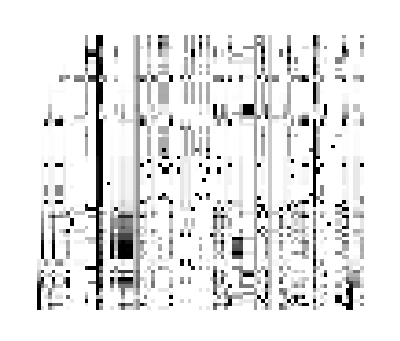

```mathematica
ArrayPlot[ForwardFlux/@fluxMinMax]
```

Generating random flux states from the min/max vectors, scaled to output = 100

```mathematica
RandomFluxState[n_]:=
Block[{f},
f=Mean[RandomChoice[fluxMinMax,n]]+0.001*Mean[fluxMinMax];
f/Total[PositivePart[MassBalance[net,f]]]*100]
```

### Check for blocked reactions

Reactions that cannot carry net flux in either direction.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,0}]//TableForm
```

<Reaction GHMT2r(rev)> | ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c | 0 | 0

Reactions that cannot carry net flux in the forward direction but in the reverse.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,_?Positive}]
```

{}

Reversible reactions that cannot carry net flux in the reverse direction.

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Intersection[
Position[Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001],0],
Position[ReversibleQ[Reactions[net]],True]]]}]
```

{{<Reaction ACONTm(rev)>,cit_m <=> icit_m},{<Reaction ASPTAm(rev)>,glu-L_m + oaa_m <=> akg_m + asp-L_m},{<Reaction ATPtm(rev)>,adp_c + atp_m <=> adp_m + atp_c},{<Reaction G3PD1(rev)>,glyc3p_c + nad_c <=> dhap_c + h_c + nadh_c},{<Reaction GHMT2r(rev)>,ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c},{<Reaction GLUNm(rev)>,gln-L_m + h2o_m <=> glu-L_m + nh4_m},{<Reaction ICDHxm(rev)>,icit_m + nad_m <=> akg_m + co2_m + nadh_m},{<Reaction LDH_L(rev)>,h_c + nadh_c + pyr_c <=> lac-L_c + nad_c},{<Reaction MDHm(rev)>,mal-L_m + nad_m <=> h_m + nadh_m + oaa_m},{<Reaction PYRt2m(rev)>,pyr_c <=> pyr_m}}

Boundary fluxes that are never non-zero.

```mathematica
Pick[InputMetabolites[net],Chop[Max/@Transpose[BoundaryUptake/@fluxMinMax],.01],0]
```

{Metabolite[arg-L,Input,Boundary],Metabolite[energy,Input,Boundary],Metabolite[pi,Input,Boundary]}

```mathematica
Pick[OutputMetabolites[net],Chop[Max/@Transpose[BoundaryRelease/@fluxMinMax],0.01],0]
```

{Metabolite[pi,Output,Boundary]}

## EMU model

### EMU decomposition

Find EMU reactions (this takes some time)

```mathematica
emuReactions=EMUAlgorithm[net,atomMap,bmap,{"C"},targets,symmetry];
Length[emuReactions]
```

964

```mathematica
emuReactionNames=EMUFluxMap[net,"reactions"];
```

```mathematica
RandomSample[emuReactions,10]
```

{EMUReaction[71,<glc-D_c{(4)}>,<g6p_c{(4)}>,1],EMUReaction[115,<asp-L_m{(24)}>,<oaa_m{(24)}>,1],EMUReaction[129,<lac-L_c{(123)}>,<pyr_c{(123)}>,1],EMUReaction[115,<asp-L_m{(4)}>,<oaa_m{(4)}>,1],EMUReaction[113,<akg_m{(4)}>,<akg_c{(4)}>,1],EMUReaction[93,<g6p_c{(56)}>,<f6p_c{(26)}>,1],EMUReaction[29,<akg_m{(2)}>,<succoa_m{(1)}>,1],EMUReaction[114,<glu-L_c{(123)}>,<akg_c{(123)}>,1],EMUReaction[37,<asp-L_m{(1234)}>,<asp-L_c{(1234)}>,1],EMUReaction[128,<akg_m{(123)}>,<icit_m{(124)}>,1]}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

497

Ensure targets are contained in EMUs

```mathematica
Complement[targets,emus]
```

{}

### Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 217 internals, 42 substrates, 0 condensations >
2 | <EMUEquation (2), 150 internals, 27 substrates, 6 condensations >
3 | <EMUEquation (3), 78 internals, 13 substrates, 5 condensations >
4 | <EMUEquation (4), 24 internals, 2 substrates, 4 condensations >
5 | <EMUEquation (5), 15 internals, 3 substrates, 2 condensations >
6 | <EMUEquation (6), 13 internals, 4 substrates, 2 condensations >

### Specify input isotopomers (tracers)

List the input metabolites that have atom information; for these the isotope distributions must be specified.

```mathematica
substrateDist=ImportMixtureID["substrate-distributions.txt"]
```

{2mop_i→NaturalIsotopomerDistribution[{4},{0.98}],ac_i→NaturalIsotopomerDistribution[{2},{0.0107}],ala-L_i→NaturalIsotopomerDistribution[{3},{0.98}],arg-L_i→NaturalIsotopomerDistribution[{6},{0.98}],asp-L_i→NaturalIsotopomerDistribution[{4},{0.98}],co2_i→NaturalIsotopomerDistribution[{1},{0.0107}],glc-D_i→NaturalIsotopomerDistribution[{6},{0.98}],gln-L_i→NaturalIsotopomerDistribution[{5},{0.98}],glucys_i→NaturalIsotopomerDistribution[{8},{0.0107}],gly_i→NaturalIsotopomerDistribution[{2},{0.98}],glyc_i→NaturalIsotopomerDistribution[{3},{0.0107}],glycogen_i→NaturalIsotopomerDistribution[{6},{0.0107}],prot_ala_i→NaturalIsotopomerDistribution[{3},{0.0107}],prot_arg_i→NaturalIsotopomerDistribution[{6},{0.0107}],ser-L_i→NaturalIsotopomerDistribution[{3},{0.98}]}

Calculate MIDs for network substrate EMUs

```mathematica
irList=Table[
Rule[e,Total[Table[
PDF[MarginalizeToMID[
FragmentIsotopomerDistribution[
MetaboliteShortName[Metabolite[e]]/.substrateDist,a]],
x],
{a,AtomNumbers[e]},{x,Tuples[Map[Range[0,Length[#]]&,a]]}]]],
{e,Flatten[SubstrateEMUs/@emuEq]}];
```

### Check: simulate steady-state mass isotopomer data

```mathematica
emuSol=EMUSimulate[emuEq,irList,EMUFluxMap[net][RandomFluxState[10]]]
```

<EMUSolution, 6 subsystems>

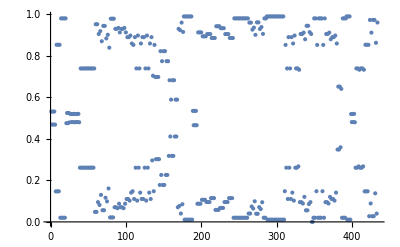
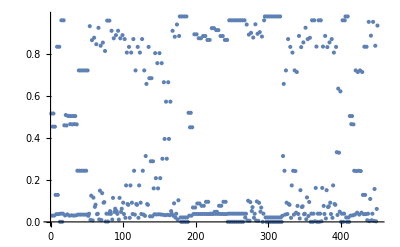
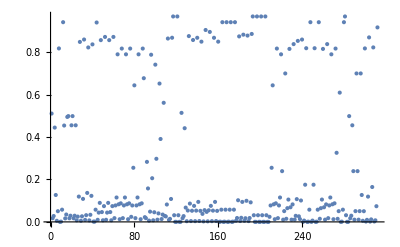
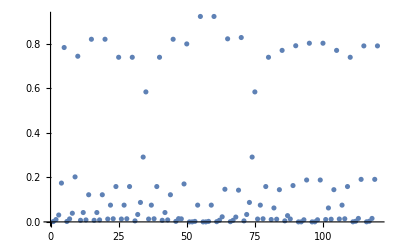
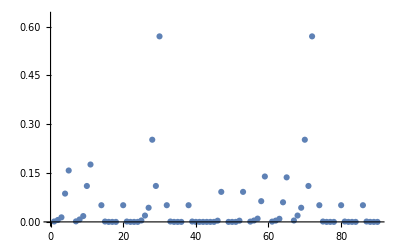
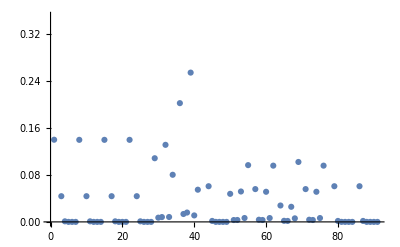

```mathematica
Table[
ListPlot[Flatten[InternalMIDs[emuSol,k]]],
{k,Length[emuEq]}]
```

```mathematica
Remove[emuSol]
```

## Analyze fluxes with GAMS, standard method

```mathematica
<<NilssonLab`GAMSFluxEstimation`
```

### Parameters

```mathematica
gamsModelName="liver-model";
```

```mathematica
gamsDir=FileNameJoin[{Directory[],"mathematica","gams"}]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport\mathematica\gams

```mathematica
If[!DirectoryQ[gamsDir],CreateDirectory[gamsDir]]
```

Here “experiments” referes to tracer settings (only one)

```mathematica
experiments={"experiment1"};
```

Smallest standard deviation allowed

```mathematica
minSD=0.01;
```

```mathematica
Directory[]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport

MIDs to fit

```mathematica
midsToFit=Block[{sampleIndex},
sampleIndex=Flatten[Position[sampleInfo,{"tissue slice 24h",_,"13C",_,Except[1],_}]];
Map[First[MIDNormalize[#]]&,measuredMIDs⟦All,sampleIndex⟧,{2}]];
```

### Generate optimization model

```mathematica
GAMSExport[gamsDir,gamsModelName,
(* model *)
net,emuReactions,emuEq,{irList},
(* measured fluxes *)
measuredBoundaryFluxeNames,Abs[mediumConcDiffMean*mediumVolume/cultureTime*10^9],mediumConcDiffSD*mediumVolume/cultureTime*10^9,
(* measured MIDs *)
experiments,measuredMetNames,{Mean/@midsToFit},{Map[Max[StandardDeviation[#],minSD]&,midsToFit]},
(* targets *)
targets,emuMixing,
RandomFluxState[10]]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport\mathematica\gams\liver-model.gms

### Run GAMS

From command line ...

### Import GAMS solutions

#### Estimated mixing matrix

```mathematica
emuMixingGams=ImportGAMSEmuMixing[gamsDir,gamsModelName,measuredMetNames,targets]
```

SparseArray[<22>, {16, 28}]

```mathematica
Block[{ij,mix},
ij=NonZeroIndices[emuMixingGams];
Transpose[{measuredMetNames⟦ij⟦All,1⟧⟧,targets⟦ij⟦All,2⟧⟧,NonZeroElements[emuMixingGams]}]]//TableForm
```

glc-D | <glc-D_c{(123456)}> | 1.
ala-L | <ala-L_c{(123)}> | 1.
arg-L | <arg-L_c{(123456)}> | 1.
asp-L | <asp-L_c{(1234)}> | 0.429457
asp-L | <asp-L_m{(1234)}> | 0.570543
gln-L | <gln-L_c{(12345)}> | 0.229561
gln-L | <gln-L_m{(12345)}> | 0.770439
ser-L | <ser-L_c{(123)}> | 1.
mal-L | <mal-L_c{(1234)}> | 0.429214
mal-L | <mal-L_m{(1234)}> | 0.570786
f6p__g1p__g6p | <f6p_c{(123456)}> | 0.178456
f6p__g1p__g6p | <g1p_r{(123456)}> | 0.821544
dhap__g3p | <dhap_c{(123)}> | 1.
orn | <orn_c{(12345)}> | 0.5
orn | <orn_m{(12345)}> | 0.5
citr-L | <citr-L_c{(123456)}> | 0.5
citr-L | <citr-L_m{(123456)}> | 0.5
glyc3p | <glyc3p_c{(123)}> | 1.
akg | <akg_c{(12345)}> | 1.
succ | <succ_m{(1234)}> | 1.
glu-L | <glu-L_c{(12345)}> | 1.
gly | <gly_c{(12)}> | 1.

#### Simulated MIDs

For all EMUs in the model

```mathematica
midGams=ImportGAMSIsotopes[gamsDir,gamsModelName,experiments,emus];
```

Check dimensions

```mathematica
Length/@midGams⟦1⟧==(EMUSize/@emus)+1
```

True

Check specific MIDs

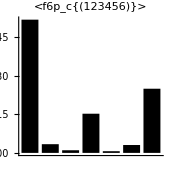
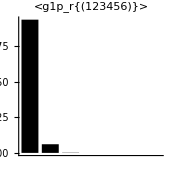
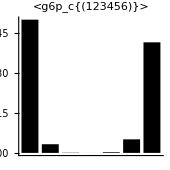
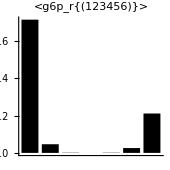
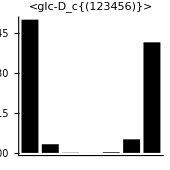
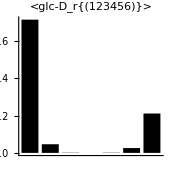

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["f6p"|"g6p"|"g1p"|"glc-D",_,_],{{{1,2,3,4,5,6}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

#### Fitted MIDs

Recover fitted MIDs as mixing x target MIDs

```mathematica
fittedMIDs=Block[{ix,mix,mid},
mix=emuMixing;
mid=midGams⟦1,ReindexList[targets,emus]⟧;
Table[
ix=Flatten[Position[em,_?Positive]];
em⟦ix⟧.mid⟦ix⟧,
{em,mix}]];
```

Compare fitted MIDs (gray) with measured (black)

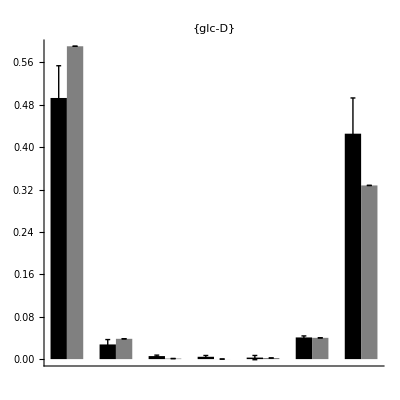
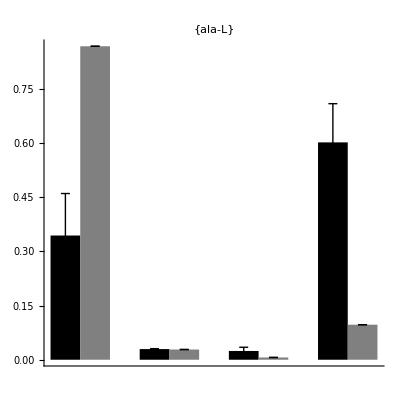
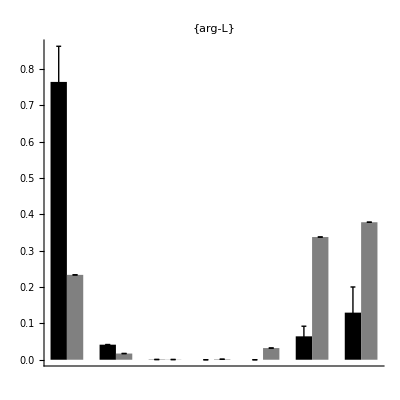
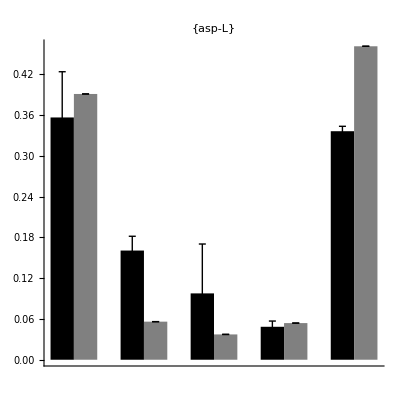
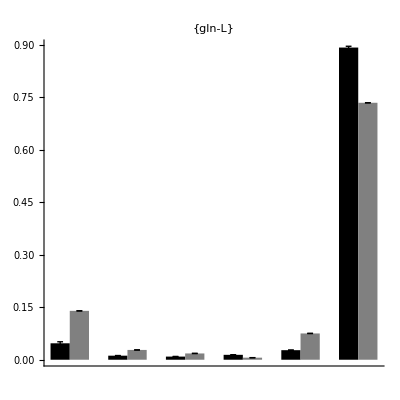
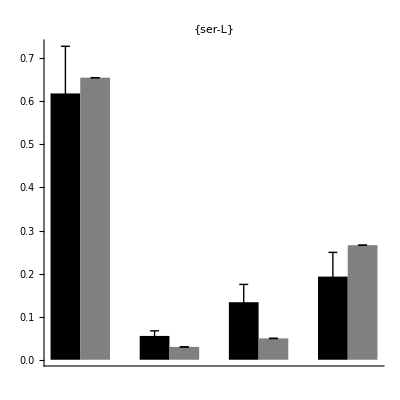
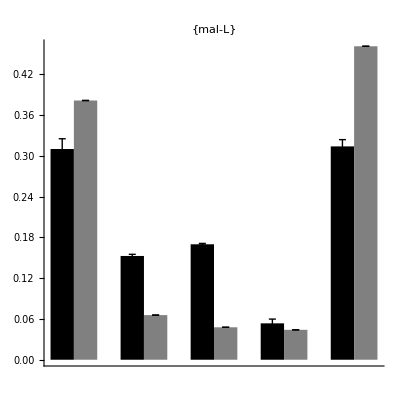
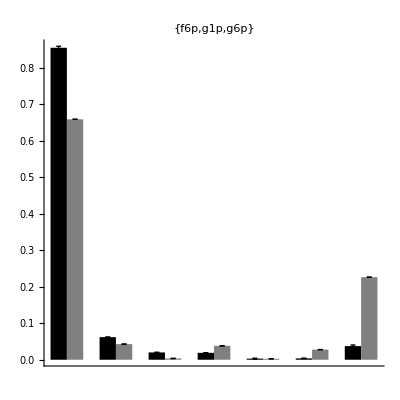

```mathematica
Table[
ErrorBarChart[
Transpose/@{midsToFit⟦i⟧,Table[fittedMIDs⟦i⟧,{3}]},
AspectRatio->1,PlotLabel->measuredMetIds⟦i⟧],
{i,Length[measuredMetIds]}]
```

Scatter plot of all fitted MIDs

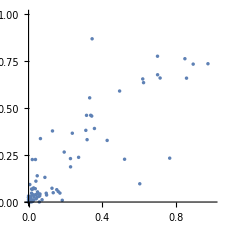

```mathematica
ListPlot[
Transpose[{Flatten[Mean/@midsToFit],Flatten[fittedMIDs]}],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

#### Fluxes

```mathematica
fluxGams=ImportGAMSFluxes[gamsDir,gamsModelName,net,EMUFluxMap[net]]
```

<FluxState, 89 reactions, 35 b. exch>

```mathematica
TableForm[
Transpose[{ForwardFlux[fluxGams],ReverseFlux[fluxGams],NetFlux[fluxGams]}],
TableHeadings->{Reactions[net],{"fwd","rev","net"}}]
```

| fwd | rev | net
<Reaction 2AMACHYD> | 0.001 | 0. | 0.001
<Reaction ACITL> | 0.001 | 0. | 0.001
<Reaction ACOAHi> | 406.257 | 0. | 406.257
<Reaction ACONTm(rev)> | 123.85 | 0.001 | 123.849
<Reaction ACRNtm> | 41.1617 | 0. | 41.1617
<Reaction ACS> | 447.418 | 0. | 447.418
<Reaction ADK1> | 447.421 | 0. | 447.421
<Reaction AKGDm(rev)> | 10000. | 9906.21 | 93.7856
<Reaction AKGtm(rev)> | 0.001 | 30.0654 | -30.0644
<Reaction ALATA_L> | 177.964 | 0. | 177.964
<Reaction ARGN> | 0.00316768 | 0. | 0.00316768
<Reaction ARGSL> | 0.00316768 | 0. | 0.00316768
<Reaction ARGSS> | 0.00316768 | 0. | 0.00316768
<Reaction ASPTA(rev)> | 10000. | 10000. | 0.001
<Reaction ASPTAm(rev)> | 0.002 | 0.001 | 0.001
<Reaction ASPtm> | 0.001 | 0. | 0.001
<Reaction ATPS4m> | 1125.97 | 0. | 1125.97
<Reaction ATPtm(rev)> | 1189.69 | 0.001 | 1189.69
<Reaction CBPSam> | 0.00316768 | 0. | 0.00316768
<Reaction CELLWORK> | 0.001 | 0. | 0.001
<Reaction CITtm> | 0.001 | 0. | 0.001
<Reaction CO2tm(rev)> | 9729.74 | 10000. | -270.259
<Reaction CRNtim> | 41.1617 | 0. | 41.1617
<Reaction CSm> | 123.85 | 0. | 123.85
<Reaction CSNATm> | 41.1617 | 0. | 41.1617
<Reaction CSNATr> | 41.1617 | 0. | 41.1617
<Reaction CYOOm> | 243.951 | 0. | 243.951
<Reaction CYOR-u10m> | 487.901 | 0. | 487.901
<Reaction ENO(rev)> | 10000. | 10000. | 0.
<Reaction FBA(rev)> | 4972.25 | 4927.93 | 44.3188
<Reaction FBP> | 37.2338 | 0. | 37.2338
<Reaction FUMm> | 93.7897 | 0. | 93.7897
<Reaction FUMtm> | 0.00316768 | 0. | 0.00316768
<Reaction G3PD1(rev)> | 10000. | 9940.74 | 59.2634
<Reaction G6PPer> | 481.819 | 0. | 481.819
<Reaction G6Pter> | 245.511 | 0. | 245.511
<Reaction GAPD(rev)> | 10000. | 9852.1 | 147.901
<Reaction GHMT2r(rev)> | 11.8896 | 11.8896 | 0.
<Reaction GLCter> | 202.573 | 0. | 202.573
<Reaction GLNtm> | 30.6934 | 0. | 30.6934
<Reaction GLUDxm(rev)> | 0.001 | 0.001 | 0.
<Reaction GLUNm(rev)> | 34.2022 | 3.50882 | 30.6934
<Reaction GLUt2m(rev)> | 9969.31 | 10000. | -30.6924
<Reaction GLYCOGEN_BREAKer> | 236.308 | 0. | 236.308
<Reaction GLYK> | 59.2634 | 0. | 59.2634
<Reaction GTHS> | 12.096 | 0. | 12.096
<Reaction H2Oter> | 481.819 | 0. | 481.819
<Reaction H2Otm(rev)> | 0.001 | 1335.47 | -1335.47
<Reaction HCO3Em> | 30.0644 | 0. | 30.0644
<Reaction HEX1> | 289.83 | 0. | 289.83
<Reaction Htm2(rev)> | 0.301464 | 1242.61 | -1242.3
<Reaction ICDHxm(rev)> | 123.85 | 0.001 | 123.849
<Reaction LDH_L(rev)> | 65.2189 | 0.00100004 | 65.2179
<Reaction MALtm> | 0.001 | 0. | 0.001
<Reaction MDH> | 0.001 | 0. | 0.001
<Reaction MDHm(rev)> | 93.7917 | 0.001 | 93.7907
<Reaction MMEm> | 0.001 | 0. | 0.001
<Reaction MMMm> | 0.001 | 0. | 0.001
<Reaction MMSAD1m> | 0.001 | 0. | 0.001
<Reaction NADH2-u10m> | 394.115 | 0. | 394.115
<Reaction NADH_REDOX> | 289.847 | 0. | 289.847
<Reaction NDPK1> | 0.001 | 0. | 0.001
<Reaction NH4tm(rev)> | 20.7279 | 51.4181 | -30.6902
<Reaction O2tm> | 243.951 | 0. | 243.951
<Reaction OCBTm> | 0.00316768 | 0. | 0.00316768
<Reaction ORNt4m> | 0.00316768 | 0. | 0.00316768
<Reaction PCm> | 30.0602 | 0. | 30.0602
<Reaction PDHm> | 82.6883 | 0. | 82.6883
<Reaction PEPCK> | 0.001 | 0. | 0.001
<Reaction PFK> | 81.5526 | 0. | 81.5526
<Reaction PGCD> | 147.901 | 0. | 147.901
<Reaction PGI(rev)> | 44.3198 | 0.001 | 44.3188
<Reaction PGK(rev)> | 10000. | 9852.1 | 147.901
<Reaction PGM(rev)> | 10000. | 10000. | 0.
<Reaction PGMTer> | 236.308 | 0. | 236.308
<Reaction PIt2m> | 1189.69 | 0. | 1189.69
<Reaction PIter> | 245.511 | 0. | 245.511
<Reaction PPA> | 447.421 | 0. | 447.421
<Reaction PPCOACm> | 0.001 | 0. | 0.001
<Reaction PROTDEG_ALA> | 159.61 | 0. | 159.61
<Reaction PROTDEG_ARG> | 0.001 | 0. | 0.001
<Reaction PSERT> | 147.901 | 0. | 147.901
<Reaction PSP_L> | 147.901 | 0. | 147.901
<Reaction PYK> | 0.001 | 0. | 0.001
<Reaction PYRt2m(rev)> | 112.749 | 0.001 | 112.748
<Reaction SERHL> | 0.001 | 0. | 0.001
<Reaction SUCD1m> | 93.7866 | 0. | 93.7866
<Reaction SUCOASm> | 93.7866 | 0. | 93.7866
<Reaction TPI(rev)> | 103.583 | 0.001 | 103.582

Boundary fluxes vs. measured

```mathematica
TableForm[
Transpose[{
BoundaryFlux[fluxGams],
BoundaryFluxNames[bnet]/.Append[Thread[Rule[measuredBoundaryFluxeNames,Abs[mediumConcDiffMean*mediumVolume/cultureTime*10^9]]],
_String->""]}],
TableHeadings->{BoundaryFluxNames[bnet],{"Fitted","Measured"}}]
```

| Fitted | Measured
2mop_IN | 0.001 | 
ac_IN | 41.1607 | 
ala-L_IN | 18.354 | 18.3605
arg-L_IN | 0.00298475 | 0.782118
asp-L_IN | 4.01854 | 4.01815
co2_IN | 1239.78 | 
energy_IN | 0.001 | 
glc-D_IN | 87.2563 | 87.2563
gln-L_IN | 30.6934 | 30.9349
glucys_IN | 12.096 | 
gly_IN | 12.096 | 11.8511
glyc_IN | 59.2634 | 
glycogen_IN | 236.308 | 
h2o_IN | 185.168 | 
h_IN | 10.4958 | 
nh4_IN | 0.001 | 
o2_IN | 243.951 | 
pi_IN | 0.001 | 
prot_ala_IN | 159.61 | 
prot_arg_IN | 0.001 | 
ser-L_IN | 1.88912 | 1.88981
arg-L_OUT | 0.00398475 | 
asp-L_OUT | 4.01537 | 
co2_OUT | 1510.04 | 
energy_OUT | 0.002 | 
glc-D_OUT | 279.246 | 
glu-L_OUT | 60.7568 | 
gthrd_OUT | 12.096 | 
h2o_OUT | 0.001 | 
h_OUT | 644.307 | 
lac-L_OUT | 65.2179 | 67.7083
nh4_OUT | 30.6922 | 
pi_OUT | 0.001 | 
ser-L_OUT | 149.789 | 
urea_OUT | 0.00316768 |